## Funciones dieléctricas de eritrocitos

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Importación de paquetes

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["KramersKronig`"]
Needs["MieTheory`"]
Needs["GoldenSectionSearchMaxMin`"]
Needs["LorentzFitSSKK`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

tolRes0=1.*^-8;
omega10=Range[0,10,0.01];
```

## Funciones generales

```mathematica
epsRe[parteRe_,parteIm_,x_]:=parteRe[x]^2-parteIm[x]^2;
epsIm[parteRe_,parteIm_,x_]:=(2*parteRe[x]*parteIm[x]);
eps[parteRe_,parteIm_,x_]:=(parteRe[x]+I parteIm[x])^2;


(*Función para que haga todo automático*)

lorentzFitSSKK[parteRe_,parteIm_,intervalos_,xmin_,xmax_,tol_,omegalist_]:=Module[{total,epsIm,epsRe,sinPico,partere2},
                                  epsIm[x_]:=Im[eps[parteRe,parteIm,x]];
                                  epsRe[x_]:=Re[eps[parteRe,parteIm,x]];
                                  sinPico=ajusteSinPico[epsIm,intervalos,tol,xmin,xmax];
                                  partere2=parteReSSKK[epsRe,sinPico[[2]],xmin,xmax,omegalist];{sinPico,partere2}];
```

## Datos beta y H2O -> Parte real

```mathematica
(*Función que da la parte real del índice de refracción a partir de la relación de Meinke 2006*)
datosH2O=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\H2O_n.csv"];
datosBeta=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\Beta_parameter_ReN_Erythrocytes.csv"];
datos1Beta=Drop[datosBeta,1];
datos1H2O=Drop[datosH2O,1];
datos2Beta=h c/datos1Beta[[All,1]];
datos2H2O=h c/(datos1H2O[[All,1]]*1000);
beta=Interpolation[Transpose[{datos2Beta,datos1Beta[[All,2]]}]]
h2o=Interpolation[Transpose[{datos2H2O,datos1H2O[[All,2]]}]];

(*Se va a encontrar la parte real empleando la relación de Meinke 2006*)
parteRe[x_,C_]:=h2o[x]*((beta[x]*C)+1);
```

InterpolatingFunction[…]

## Concentración 28.7 g/dL

```mathematica
(*Se van a importar los datos de la parte real e imaginaria del índice de refracción*)
datos0Im=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\28.7_k_ImN_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1Im=Drop[datos0Im,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2Im=h c/datos1Im[[All,1]];
(*Se interpolan los datos de la parte imaginaria y real*)
parteIm280=Transpose[{datos2Im,datos1Im[[All,2]]}];
parteIm287=Interpolation[parteIm280,InterpolationOrder->1];

parteRe287[x_]:=parteRe[x,28.7];
```

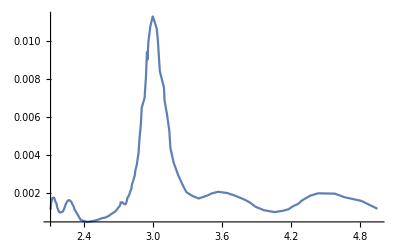

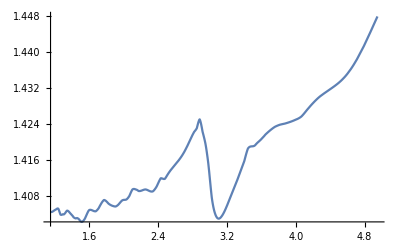

```mathematica
Plot[parteIm28[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe287[x],{x,1.15,4.95},PlotRange->All]
```

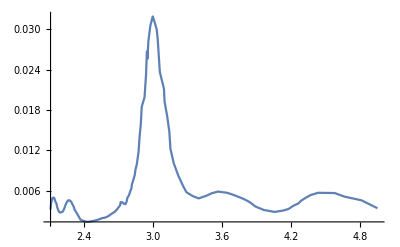

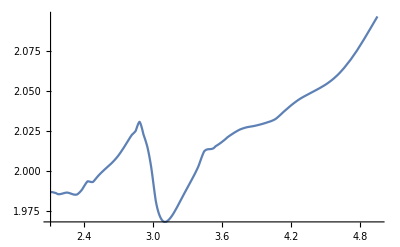

```mathematica
(*Función dieléctrica experimental*)
eps287Im[x_]:=Im[eps[parteRe287,parteIm287,x]];
eps287Re[x_]:=Re[eps[parteRe287,parteIm287,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos287={{2.1,2.2},{2.2,2.4},{2.8,3.3},{3.5,3.8},{4,4.7}};

{xmin287,xmax287}={Min[datos2Im],Max[datos2Im]};

Plot[eps287Im[x],{x,2.11,4.95},PlotRange->All]
Plot[eps287Re[x],{x,2.11,4.95},PlotRange->All]
```

```mathematica
fitSSKK287=lorentzFitSSKK[parteRe287,parteIm287,intervalos287,xmin287,xmax287,1.*^-8,omega10];
```

Set::setraw: Cannot assign to raw object {1.14551,1.15551,1.16551,1.17551,1.18551,1.19551,1.20551,1.21551,1.22551,1.23551,«364»}.

Set::setraw: Cannot assign to raw object 0.000161198.

Set::setraw: Cannot assign to raw object 0.00016341.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

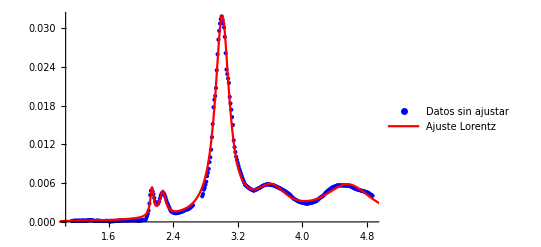

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.12713} lies outside the range of data in the interpolating function. Extrapolation will be used.

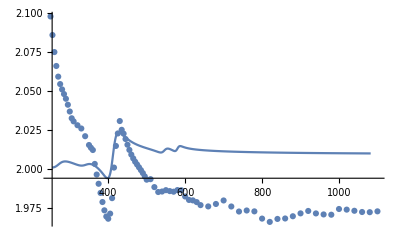

2.8

```mathematica
Show[ListPlot[fitSSKK287[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK287[[1]][[2]][ω],{ω,xmin287-0.5,xmax287+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps287DataRe=Table[{x,eps287Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp287sskk=Plot[fitSSKK287[[2]][[3]][h c/λ],{λ,h c/xmax287,h c/xmin287}];

plotpoints287sskk=ListPlot[{#[[1]],#[[2]]}&/@eps287DataRe];

sskk287=Show[{interp287sskk,plotpoints287sskk}, PlotRange->All]

fitSSKK287[[2]][[1]]
```

## Concentración 29.2 g/dL

```mathematica
parteRe292[x_]:=parteRe[x,29.2];
parteIm292[x_]:=(29.2/28.7)*parteIm28[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps292Im[x_]:=Im[eps[parteRe292,parteIm292,x]];
eps292Re[x_]:=Re[eps[parteRe292,parteIm292,x]];
```

```mathematica
fitSSKK292=lorentzFitSSKK[parteRe292,parteIm292,intervalos287,xmin287,xmax287,1.*^-8,omega10];
```

Set::setraw: Cannot assign to raw object {1.14551,1.15551,1.16551,1.17551,1.18551,1.19551,1.20551,1.21551,1.22551,1.23551,«364»}.

Set::setraw: Cannot assign to raw object 0.000164162.

Set::setraw: Cannot assign to raw object 0.000166414.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

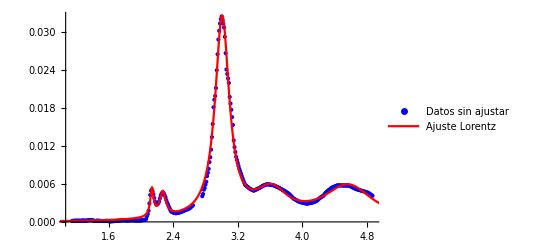

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.12713} lies outside the range of data in the interpolating function. Extrapolation will be used.

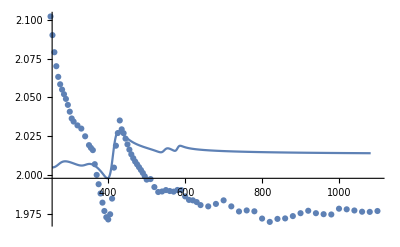

2.8

```mathematica
Show[ListPlot[fitSSKK292[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK292[[1]][[2]][ω],{ω,xmin287-0.5,xmax287+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps292DataRe=Table[{x,eps292Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp292sskk=Plot[fitSSKK292[[2]][[3]][h c/λ],{λ,h c/xmax287,h c/xmin287}];

plotpoints292sskk=ListPlot[{#[[1]],#[[2]]}&/@eps292DataRe];

sskk292=Show[{interp292sskk,plotpoints292sskk}, PlotRange->All]

fitSSKK292[[2]][[1]]
```

## Concentración 30 g/dL

```mathematica
parteRe30[x_]:=parteRe[x,30];
parteIm30[x_]:=(30/28.7)*parteIm28[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps30Im[x_]:=Im[eps[parteRe30,parteIm30,x]];
eps30Re[x_]:=Re[eps[parteRe30,parteIm30,x]];
```

```mathematica
fitSSKK30=lorentzFitSSKK[parteRe30,parteIm30,intervalos287,xmin287,xmax287,1.*^-8,omega10];
```

Set::setraw: Cannot assign to raw object {1.14551,1.15551,1.16551,1.17551,1.18551,1.19551,1.20551,1.21551,1.22551,1.23551,«364»}.

Set::setraw: Cannot assign to raw object 0.000168916.

Set::setraw: Cannot assign to raw object 0.000171233.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

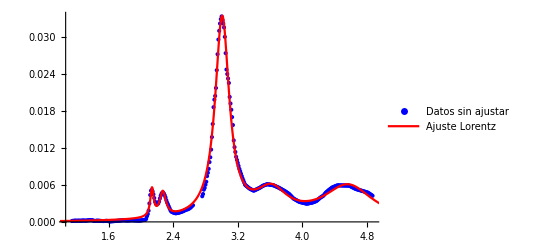

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.12713} lies outside the range of data in the interpolating function. Extrapolation will be used.

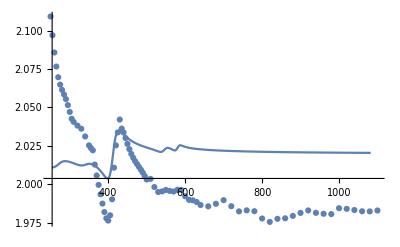

2.8

```mathematica
Show[ListPlot[fitSSKK30[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK30[[1]][[2]][ω],{ω,xmin287-0.5,xmax287+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps30DataRe=Table[{x,eps30Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp30sskk=Plot[fitSSKK30[[2]][[3]][h c/λ],{λ,h c/xmax287,h c/xmin287}];

plotpoints30sskk=ListPlot[{#[[1]],#[[2]]}&/@eps30DataRe];

sskk30=Show[{interp30sskk,plotpoints30sskk}, PlotRange->All]

fitSSKK30[[2]][[1]]
```

## Concentración 30.6 g/dL

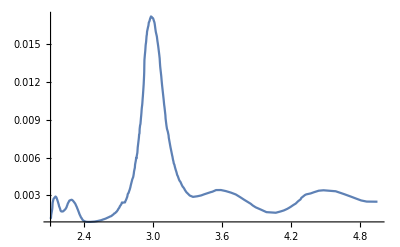

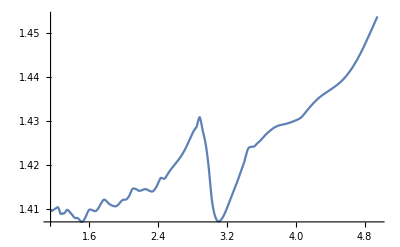

```mathematica
datosuA30=Import["C:\\Users\\danal\\Documents\\Grupo_Nanoplasmónica\\Tesis\\Refractive index\\30.6_uA_Erythrocytes.csv"];
(*Se eliminan los encabezados de los datos*)
datos1uA30=Drop[datosuA30,1];
(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
datos2im30=h c/datos1uA30[[All,1]];
(*Obtener la parte imaginariad del índice de refracción a partir del coeficiente de absorción*)
datos3im30=datos1uA30[[All,2]]*10^(-6)*datos1uA30[[All,1]]/(4*Pi);
(*Se interpolan los datos de la parte imaginaria*)
parteIm300=Transpose[{datos1uA30[[All,1]],datos3im30}];
parteIm306=Interpolation[Transpose[{datos2im30,datos3im30}],InterpolationOrder->1];
parteRe306[x_]:=parteRe[x,30.6]

Plot[parteIm306[x],{x,2.11,4.95},PlotRange->All]
Plot[parteRe306[x],{x,1.15,4.95},PlotRange->All]
```

```mathematica
(*Función dieléctrica experimental*)
eps306Im[x_]:=Im[eps[parteRe306,parteIm306,x]];
eps306Re[x_]:=Re[eps[parteRe306,parteIm306,x]];
(*Intervalos de búsqueda de los máximos*)
intervalos306={{2.07,2.1},{2.15,2.4},{2.8,3.2},{3.4,3.7},{4.2,4.7}};
{xmin306,xmax306}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK306=lorentzFitSSKK[parteRe306,parteIm306,intervalos306,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00199574.

Set::setraw: Cannot assign to raw object 0.00221515.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

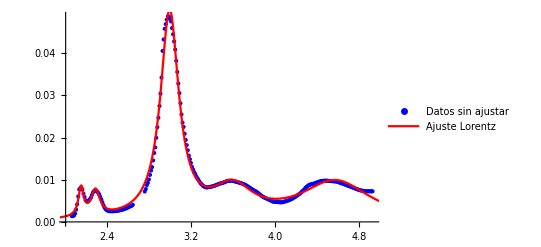

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

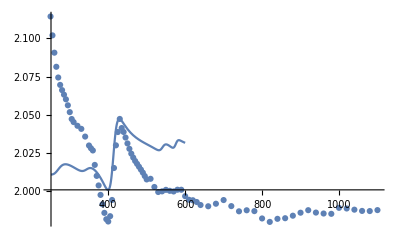

2.88

```mathematica
Show[ListPlot[fitSSKK306[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK306[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps306DataRe=Table[{x,eps306Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp306sskk=Plot[fitSSKK306[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints306sskk=ListPlot[{#[[1]],#[[2]]}&/@eps306DataRe];

sskk30=Show[{interp306sskk,plotpoints306sskk}, PlotRange->All]

fitSSKK306[[2]][[1]]
```

## Concentración 30.8 g/dL

```mathematica
parteRe308[x_]:=parteRe[x,30.8];
parteIm308[x_]:=(30.8/28.7)*parteIm287[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps308Im[x_]:=Im[eps[parteRe308,parteIm308,x]];
eps308Re[x_]:=Re[eps[parteRe308,parteIm308,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK308=lorentzFitSSKK[parteRe308,parteIm308,intervalos308,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00200954.

Set::setraw: Cannot assign to raw object 0.00223047.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

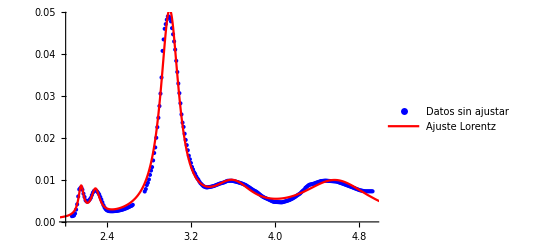

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

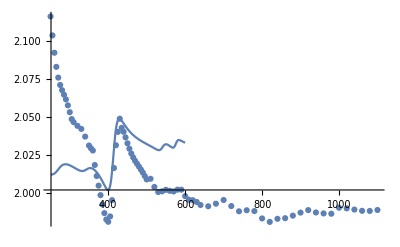

2.88

```mathematica
Show[ListPlot[fitSSKK308[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK308[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps308DataRe=Table[{x,eps308Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp308sskk=Plot[fitSSKK308[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints308sskk=ListPlot[{#[[1]],#[[2]]}&/@eps308DataRe];

sskk308=Show[{interp308sskk,plotpoints308sskk}, PlotRange->All]

fitSSKK308[[2]][[1]]
```

## Concentración 31.6 g/dL

```mathematica
parteRe316[x_]:=parteRe[x,31.6];
parteIm316[x_]:=(31.6/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps316Im[x_]:=Im[eps[parteRe316,parteIm316,x]];
eps316Re[x_]:=Re[eps[parteRe316,parteIm316,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK316=lorentzFitSSKK[parteRe316,parteIm316,intervalos306,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00206484.

Set::setraw: Cannot assign to raw object 0.00229185.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

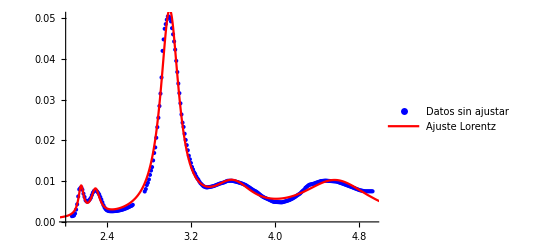

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

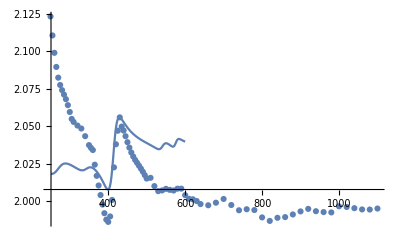

2.88

```mathematica
Show[ListPlot[fitSSKK316[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK316[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps316DataRe=Table[{x,eps316Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp316sskk=Plot[fitSSKK316[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints316sskk=ListPlot[{#[[1]],#[[2]]}&/@eps316DataRe];

sskk316=Show[{interp316sskk,plotpoints316sskk}, PlotRange->All]

fitSSKK316[[2]][[1]]
```

## Concentración 32.4 g/dL

```mathematica
parteRe324[x_]:=parteRe[x,32.4];
parteIm324[x_]:=(32.4/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps324Im[x_]:=Im[eps[parteRe324,parteIm324,x]];
eps324Re[x_]:=Re[eps[parteRe324,parteIm324,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK324=lorentzFitSSKK[parteRe324,parteIm324,intervalos308,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.0021203.

Set::setraw: Cannot assign to raw object 0.00235341.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

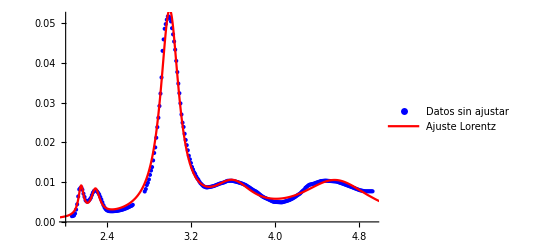

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

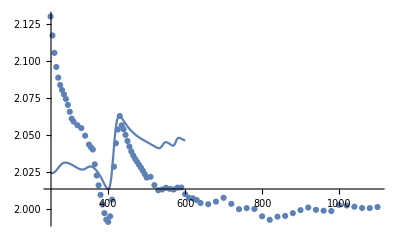

2.88

```mathematica
Show[ListPlot[fitSSKK324[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK324[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps324DataRe=Table[{x,eps324Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp324sskk=Plot[fitSSKK324[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints324sskk=ListPlot[{#[[1]],#[[2]]}&/@eps324DataRe];

sskk324=Show[{interp324sskk,plotpoints324sskk}, PlotRange->All]

fitSSKK324[[2]][[1]]
```

## Concentración 33.2 g/dL

```mathematica
parteRe332[x_]:=parteRe[x,33.2];
parteIm332[x_]:=(33.2/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps332Im[x_]:=Im[eps[parteRe332,parteIm332,x]];
eps332Re[x_]:=Re[eps[parteRe332,parteIm332,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK332=lorentzFitSSKK[parteRe332,parteIm332,intervalos308,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00217591.

Set::setraw: Cannot assign to raw object 0.00241514.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

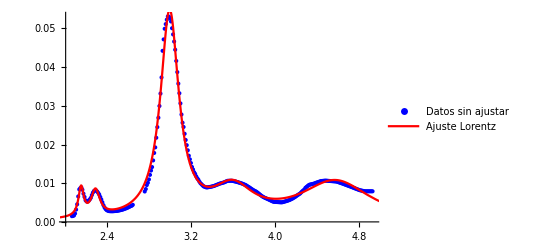

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

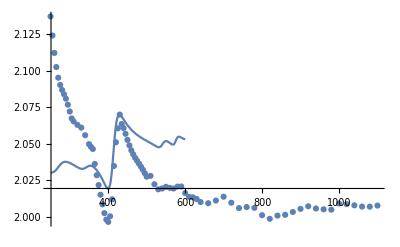

2.88

```mathematica
Show[ListPlot[fitSSKK332[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK332[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps332DataRe=Table[{x,eps332Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp332sskk=Plot[fitSSKK332[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints332sskk=ListPlot[{#[[1]],#[[2]]}&/@eps332DataRe];

sskk332=Show[{interp332sskk,plotpoints332sskk}, PlotRange->All]

fitSSKK332[[2]][[1]]
```

## Concentración 34 g/dL

```mathematica
parteRe34[x_]:=parteRe[x,34];
parteIm34[x_]:=(34/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps34Im[x_]:=Im[eps[parteRe34,parteIm34,x]];
eps34Re[x_]:=Re[eps[parteRe34,parteIm34,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK34=lorentzFitSSKK[parteRe34,parteIm34,intervalos308,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00223168.

Set::setraw: Cannot assign to raw object 0.00247705.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

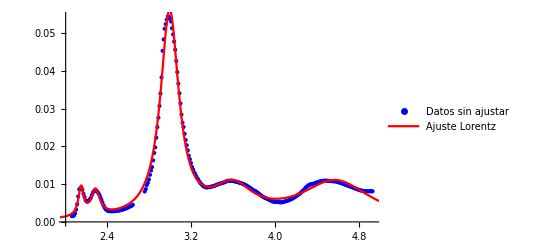

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

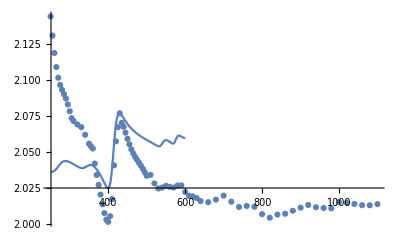

2.88

```mathematica
Show[ListPlot[fitSSKK34[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK34[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps34DataRe=Table[{x,eps34Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp34sskk=Plot[fitSSKK34[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints34sskk=ListPlot[{#[[1]],#[[2]]}&/@eps34DataRe];

sskk34=Show[{interp34sskk,plotpoints34sskk}, PlotRange->All]

fitSSKK34[[2]][[1]]
```

## Concentración 34.8 g/dL

```mathematica
parteRe348[x_]:=parteRe[x,34.8];
parteIm348[x_]:=(34.8/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps348Im[x_]:=Im[eps[parteRe348,parteIm348,x]];
eps348Re[x_]:=Re[eps[parteRe348,parteIm348,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos308={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin308,xmax308}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK348=lorentzFitSSKK[parteRe348,parteIm348,intervalos308,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.00228761.

Set::setraw: Cannot assign to raw object 0.00253913.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

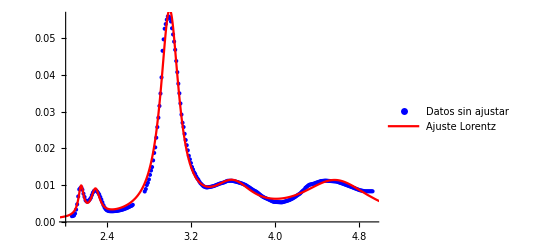

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

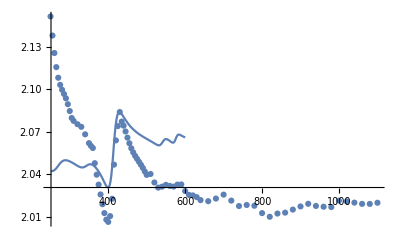

2.88

```mathematica
Show[ListPlot[fitSSKK348[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK348[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps348DataRe=Table[{x,eps348Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp348sskk=Plot[fitSSKK348[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints348sskk=ListPlot[{#[[1]],#[[2]]}&/@eps348DataRe];

sskk348=Show[{interp348sskk,plotpoints348sskk}, PlotRange->All]

fitSSKK348[[2]][[1]]
```

## Concentración 35.6 g/dL

```mathematica
parteRe356[x_]:=parteRe[x,35.6];
parteIm356[x_]:=(35.6/30.6)*parteIm306[x];
```

```mathematica
(*Función dieléctrica experimental*)
eps356Im[x_]:=Im[eps[parteRe356,parteIm356,x]];
eps356Re[x_]:=Re[eps[parteRe356,parteIm356,x]];

(*Intervalos de búsqueda de los máximos*)
intervalos356={{2.1,2.2},{2.2,2.4},{2.9,2.32},{3.5,3.8},{4,4.7}};
{xmin356,xmax356}={Min[datos2im30],Max[datos2im30]};
```

```mathematica
fitSSKK356=lorentzFitSSKK[parteRe356,parteIm356,intervalos306,xmin306,xmax306,1.*^-8,omega10];
```

InterpolatingFunction::dmval: Input value {2.05} lies outside the range of data in the interpolating function. Extrapolation will be used.

Set::setraw: Cannot assign to raw object {2.0664,2.0764,2.0864,2.0964,2.1064,2.1164,2.1264,2.1364,2.1464,2.1564,«277»}.

Set::setraw: Cannot assign to raw object 0.0023437.

Set::setraw: Cannot assign to raw object 0.00260138.

General::stop: Further output of Set::setraw will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {2.06} lies outside the range of data in the interpolating function. Extrapolation will be used.

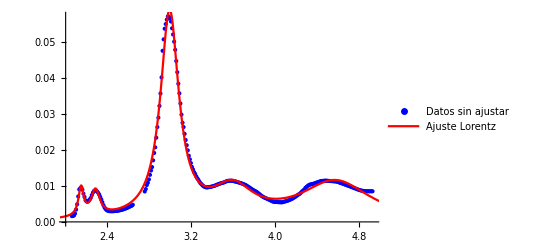

InterpolatingFunction::dmval: Input value {4.95937} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2.03253} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.99975} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

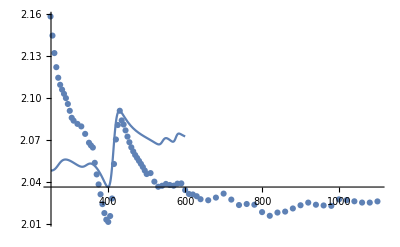

2.88

```mathematica
Show[ListPlot[fitSSKK356[[1]][[1]],PlotStyle->Blue,PlotLegends->{"Datos sin ajustar"},PlotRange->All],
            Plot[fitSSKK356[[1]][[2]][ω],{ω,xmin306-0.5,xmax306+0.5},PlotStyle->{Thick,Red},PlotLegends->{"Ajuste Lorentz"},PlotRange->All]]

eps356DataRe=Table[{x,eps356Re[h c/x]},{x,datos1Beta[[All,1]]}];

interp356sskk=Plot[fitSSKK356[[2]][[3]][h c/λ],{λ,h c/xmax306,h c/xmin306}];

plotpoints356sskk=ListPlot[{#[[1]],#[[2]]}&/@eps356DataRe];

sskk356=Show[{interp356sskk,plotpoints356sskk}, PlotRange->All]

fitSSKK356[[2]][[1]]
```

```mathematica
Plot[{fitSSKK292[[1]][[2]][h c/l],fitSSKK30[[1]][[2]][h c/l],fitSSKK308[[1]][[2]][h c/l],fitSSKK316[[1]][[2]][h c/l],fitSSKK324[[1]][[2]][h c/l],
      fitSSKK332[[1]][[2]][h c/l],fitSSKK34[[1]][[2]][h c/l],fitSSKK348[[1]][[2]][h c/l],fitSSKK356[[1]][[2]][h c/l]},{l, 400,600},PlotRange->All]
```

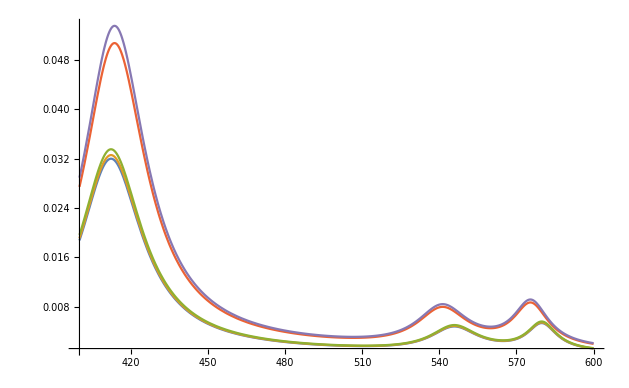

```mathematica
Plot[{fitSSKK287[[1]][[2]][h c/l],fitSSKK292[[1]][[2]][h c/l],fitSSKK30[[1]][[2]][h c/l],fitSSKK308[[1]][[2]][h c/l],fitSSKK324[[1]][[2]][h c/l]},{l, 400,600},PlotRange->All]
```

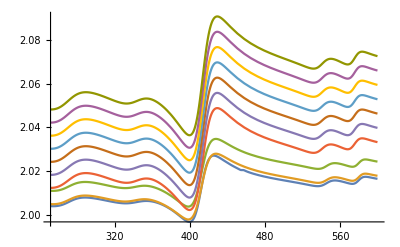

```mathematica
Plot[{partere282[h c/λ],fitSSKK292[[2]][[3]][h c/λ],fitSSKK30[[2]][[3]][h c/λ],fitSSKK308[[2]][[3]][h c/λ],fitSSKK316[[2]][[3]][h c/λ],fitSSKK324[[2]][[3]][h c/λ],
      fitSSKK332[[2]][[3]][h c/λ],fitSSKK34[[2]][[3]][h c/λ],fitSSKK348[[2]][[3]][h c/λ],fitSSKK356[[2]][[3]][h c/λ]},{λ,h c/xmax306,h c/xmin306}]
```